# Cantor Pairing Function

Juan Antonio Villegas Recio

En este documento implementamos la función de paridad de Cantor π (Cantor Pairing Function, a menudo referida en este documento como CPF), así como su inversa π^-1. Creamos también una lista de números naturales asociados a su pareja y a los monomios x^a y^b asociados a dicha pareja.

### Implementación de la CPF

```mathematica
(* CANTOR PAIRING FUNCTION, implementada de dos maneras distintas:
	- Una acepta como argumento una pareja de números naturales
   - La otra acepta dos números naturales como argumentos.
Devuelve un número natural z tal que z = π(n,m)
*)
CPF[{n_,m_}]:= (1/2)(n+m)(n+m+1)+m;
CPF[n_,m_]:=CPF[{n,m}];

(* INVERSE OF CANTOR PAIRING FUNCTION, acepta un número natural z como argumento
Devuelve una pareja {x,y} tal que (x,y) = π^-1(z)
*)
CPFinv[n_]:=Block[{w,x,y,t},
w = Floor[(Sqrt[8*n+1]-1)/2];
t = (w*w+w)/2;
y = n-t;
x = w-y;
Return[{x,y}]
]
```

Comprobamos que, en efecto, son inversas

```mathematica
Table[CPF[CPFinv[n]], {n,0,20}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

### Tabla de números naturales y su pareja y monomio asociados

```mathematica
For[i=0, i<= 30, i++,
par = CPFinv[i];
Print[ToString[i] <>  ": " <> ToString[x^par[[1]] y^par[[2]], FormatType->StandardForm] <> ", " <> ToString[par]]
]
```

0: 1, {0, 0}

1: x, {1, 0}

2: y, {0, 1}

3: x^2, {2, 0}

4: x y, {1, 1}

5: y^2, {0, 2}

6: x^3, {3, 0}

7: x^2 y, {2, 1}

8: x y^2, {1, 2}

9: y^3, {0, 3}

10: x^4, {4, 0}

11: x^3 y, {3, 1}

12: x^2 y^2, {2, 2}

13: x y^3, {1, 3}

14: y^4, {0, 4}

15: x^5, {5, 0}

16: x^4 y, {4, 1}

17: x^3 y^2, {3, 2}

18: x^2 y^3, {2, 3}

19: x y^4, {1, 4}

20: y^5, {0, 5}

21: x^6, {6, 0}

22: x^5 y, {5, 1}

23: x^4 y^2, {4, 2}

24: x^3 y^3, {3, 3}

25: x^2 y^4, {2, 4}

26: x y^5, {1, 5}

27: y^6, {0, 6}

28: x^7, {7, 0}

29: x^6 y, {6, 1}

30: x^5 y^2, {5, 2}

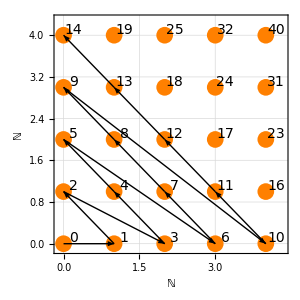

```mathematica
(* GRÁFICO *)
n=4; (*número de elementos a graficar*)

data=Table[Table[{k-i,i,CPF[k-i,i]},{i,0,k}],{k,0,n}];

pairs=Partition[Flatten[data,1],3];

points=Most/@Flatten[data,1];
extrapoints =  {{4,1},{4,2},{4,3},{4,4},{3,2},{3,3},{3,4},{2,3},{2,4},{1,4}};
labels = Join[Table[Text[Style[CPF[points[[i]][[1]],points[[i]][[2]]], FontSize->14],points[[i]]+{0.2,0.1}], {i,1,Length[points]}], Table[Text[Style[CPF[extrapoints[[i]][[1]],extrapoints[[i]][[2]]], FontSize->14],extrapoints[[i]]+{0.2,0.1}], {i,1,Length[extrapoints]}]];

arrows=Arrow/@Partition[points,2,1];

Show[ListPlot[Join[points,extrapoints],PlotStyle->{Orange, PointSize[0.04]},AspectRatio->1 ,ImageSize->300,PlotRange->{{-0.1,4.35},{-0.1,4.3}}, GridLines->Automatic, LabelStyle->Directive[FontSize->14]],Graphics[{EdgeForm[{Red,Thickness[0.06]}],Arrowheads[Medium],arrows,labels}],Frame->True, FrameLabel->{"ℕ","ℕ"}]
```

```mathematica
Show[%587,Background->None]
```

-Graphics-

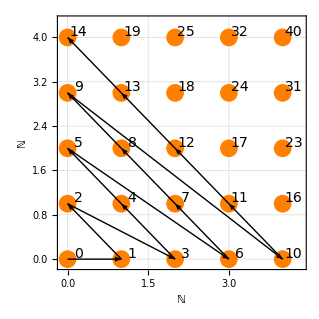

```mathematica
Show[%588,Background->None]
```

```mathematica
Export["transparent.png",%,Background->None]
```

transparent.png